```mathematica
Clear["Global`*"]

(* 2nd test *)
paperData2={
{12.5,2.8,2.3,18.1,0.2,0.2},
{29.7,7.3,6.4,27.6,1.9,1.9},
{4.4,4.8,4.5,6.6,0.9,0.9},
{4.6,2.8,2.4,4.6,0.7,0.7},
{1.6,1.1,0.9,0.75,0.15,0.15},
{10.6,4.7,4.2,4.8,1.0,1.0},
{1.9,0.9,0.7,0.81,0.16,0.16},
{1.7,1.7,1.5,0.4,0.16,0.16},
{9.8,4.3,3.5,4.58,0.15,0.18},
{0.2,0.9,0.7,0.63,0.03,0.06},
{0.3,0.5,0.4,0.59,0.04,0.05}
};(* theoretical uncertainty of A-B (line 8) is assumed to be same with A+B (line 7) *)
(* experimental correlation - 1st test: no correlation on 8th channel *)
expCorr1=({{1, -0.41, 0.06, -0.11, -0.23, -0.18, -0.4, 0, -0.48, 0.02, -0.07}, {-0.41, 1, -0.39, 0.09, 0.17, 0.04, 0.18, 0, 0.2, -0.04, 0.05}, {0.06, -0.39, 1, -0.04, -0.05, 0.02, 0.01, 0, -0.1, -0.01, -0.02}, {-0.11, 0.09, -0.04, 1, 0.12, -0.13, 0.1, 0, -0.08, -0.03, 0.03}, {-0.23, 0.17, -0.05, 0.12, 1, -0.1, 0.08, 0, 0.02, -0.03, 0.05}, {-0.18, 0.04, 0.02, -0.13, -0.1, 1, -0.03, 0, -0.35, -0.02, -0.03}, {-0.4, 0.18, 0.01, 0.1, 0.08, -0.03, 1, 0, 0.16, -0.03, -0.03}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {-0.48, 0.02, -0.1, -0.08, 0.02, -0.35, 0.16, 0, 1, 0, 0.05}, {0.02, -0.04, -0.01, -0.03, -0.03, -0.02, -0.03, 0, 0, 1, -0.11}, {-0.07, 0.05, -0.02, 0.03, 0.05, -0.03, -0.03, 0, 0.05, -0.11, 1}});
thCorr1=IdentityMatrix[11];
thCorr3=Table[0,{i,1,11},{j,1,11}];
(* Parametirized all the channels *)
cgammap=16*(3.1416)^2*cA;
cgp=16*(3.1416)^2*cG;
cgamma=0.357^2/0.080^2 cA;
cWW=0.5*T;
cB=-0.5*T;
muZZ1=1-(10cWW+3.7cHW-5.8cgammap+56cgp+2.3 cu^2+8.4 cgammap^2+790 cgp^2+26 cWW^2+3.8 cHW^2+cWW*19*cHW);
muZZ2=1+55cWW+13cB+15cHW+0.018cgamma-(0.17cu+cWW+0.37 cHW+1.6 cgp)+28 cWW^2+3.5 cB^2+2.2 cHW^2+cWW(10cB+15cHW)+cB(3.8cHW+0.052cgammap)-(0.13 cu^2+2.6 cWW^2+4.7 cHW^2+23 cgp^2+cWW(0.11cB+1.9cHW)+cHW(0.03*cB+0.1cgamma));
ParaTable=Table[0,{i,1,11}];
ParaTable[[1]]=1+(-5.8*cgammap)+8.4*cgammap^2-(55*cWW+13*cB+15cHW+0.018*cgamma)-(28 cWW^2+3.5 cB^2+2.2 cHW^2+cWW(10cB+15 cHW)+cB(3.8cHW+0.052*cgammap))//Expand;
ParaTable[[2]]=1+56 cgp+780 cgp^2//Expand;
ParaTable[[3]]=1+56 cgp+780 cgp^2//Expand;
ParaTable[[4]]=1+56 cgp+780 cgp^2//Expand;
ParaTable[[5]]=1+56cgp+780 cgp^2//Expand;
ParaTable[[6]]=1+56*cgp+780*cgp^2//Expand;
ParaTable[[7]]=1+0.57*(56*cgp+780*cgp^2)*(1-0.205/0.81)+0.16*(1.5*cWW-0.025*cB-3.6cHW+11*cWW^2+0.22*cB^2+12 cHW^2+cWW*(0.91*cB+3.4*cHW)+cB*(0.42 cHW))*(1-0.605/8.1)//Expand;
ParaTable[[8]]=1+0.57*(56*cgp+780*cgp^2)*(1+0.205/0.4)-0.16*(1.5*cWW-0.025*cB-3.6cHW+11*cWW^2+0.22*cB^2+12 cHW^2+cWW*(0.91*cB+3.4*cHW)+cB*(0.42 cHW))*(1-0.605/0.4)//Expand;
ParaTable[[9]]=1+(1.3*cWW-0.023*cB-4.3cHW+1.2*cWW-0.027*cB-5.8cHW+7.8*cWW-0.19*cB-31cHW+1.4*cWW-0.028*cB-6.2cHW)+(6.8*cWW^2+0.17*cB^2+11 cHW^2+cWW*(0.52*cB+0.79cHW)+cB*(0.19*cHW))+(7.7*cWW^2+0.22*cB^2+20 cHW^2+cWW*(0.61*cB+7.7cHW)+cB*0.67*cHW+5.4*10^2*cWW^2+11*cB^2+6.3*10^2*cHW^2+cWW*(69*cB+10^3*cHW)+cB*68*cHW+12*cWW^2+0.3*cB^2+30 cHW^2+cWW*(1.4cB+17cHW)+cB*1.3*cHW)//Expand;
ParaTable[[10]]=1+0.535*(34 cWW+11cHW+310 cWW^2+61 cHW^2+cWW*230*cHW)+0.5*0.066*(76cWW+51cHW+1600 cWW^2+870 cHW^2)+0.5*0.066*(71cWW+46cHW+1500 cWW^2+800 cHW^2+2000 cWW cHW)+0.021*(200cWW+170cHW+16000 cWW^2+14000 cHW^2+30000cWW cHW)+0.313*(30cWW+8.4cB+8.5cHW+0.032cgamma+240 cWW^2+20 cB^2+34 cHW^2+cWW(140cB+150cHW+0.5cgamma)+cB(42cHW))+0.5*0.051*(62cWW+18cB+38cHW+1000 cWW^2+90 cB^2+480 cHW^2+cWW(610cB+1300cHW)+cB(380cHW))+0.5*0.051*(58cWW+17cB+33cHW+960 cWW^2+82 cB^2+440 cHW^2+cWW(560cB+1200cHW)+cB(330cHW))+0.014*(150cWW+46cB+130cHW+9600 cWW^2+850 cB^2+8000 cHW^2+cWW(5700cB+17000 cHW)+cB(5100cHW))//Expand;
ParaTable[[11]]=1+2.9cu+0.93cgp+2.1 cu^2;
(* Choose 1st or 2nd test *)
paperData=paperData2;
expCorr=expCorr1;
thCorr=thCorr2;
muZZ=muZZ1;
For[i=2,i<=11,i++,
ParaTable[[i]]=ParaTable[[i]]*muZZ//Expand
];
muhat=Table[paperData[[i,1]],{i,1,11}];
muSM=Table[paperData[[i,4]],{i,1,11}];
(* Variable Gaussian *)
(*expVGau=Table[paperData[[i,2]]*paperData[[i,3]],{i,1,11}];
expVGauPrime=Table[paperData[[i,2]]-paperData[[i,3]],{i,1,11}];
thVGau=Table[paperData[[i,5]]*paperData[[i,6]],{i,1,11}];
thVGauPrime=Table[paperData[[i,5]]-paperData[[i,6]],{i,1,11}];*)
(*Gaussian*)
expVGau=Table[(paperData[[i,2]]+paperData[[i,3]])/2,{i,1,11}];
expVGauPrime=Table[0,{i,1,11}];
thVGau=Table[(paperData[[i,5]]+paperData[[i,6]])/2,{i,1,11}];
thVGauPrime=Table[0,{i,1,11}];
(*---*)
rule={cG->a*10^-4,cA->b*10^-4,cu->c,cHW->d*10^-1,T->e*10^-1};
```

```mathematica
L=10000;
n=10;
ai=-1;af=1;
bi=-1;bf=1;
ci=-1;cf=1;
di=-1;df=1;
ei=-1;ef=1;
da=1.0*(af-ai)/n;
db=1.0*(bf-bi)/n;
dc=1.0*(cf-ci)/n;
dd=1.0*(df-di)/n;
de=1.0*(ef-ei)/n;

bestFit={-1,-1,-1,-1,-1};
For[a=ai,a<=af,a=a+da,
Print["a=",a];
For[b=bi,b<=bf,b=b+db,
For[c=ci,c<=cf,c=c+dc,
For[d=di,d<=df,d=d+dd,
For[e=ei,e<=ef,e=e+de,
mueft=muSM*ParaTable/.rule;
muvec=mueft-muhat;
expUncSym=Sqrt[Abs[expVGau+expVGauPrime*muvec]];
expCov=Table[expCorr[[j,k]]*expUncSym[[j]]*expUncSym[[k]],{j,1,11},{k,1,11}];
thUncSym=Sqrt[Abs[thVGau+thVGauPrime*muvec]];
thCov=Table[thCorr[[j,k]]*expUncSym[[j]]*expUncSym[[k]],{j,1,11},{k,1,11}];
cov=expCov+thCov;
invCov=Inverse[cov];
LogL=muvec.invCov.muvec;
If[LogL<L,L=LogL;bestFit={a,b,c,d,e}]
]
]
]
]
]
Print["scanning done"]
Print["best fit at ",bestFit]
```

a=-1

a=-0.8

a=-0.6

a=-0.4

a=-0.2

a=-5.55112×10^-17

a=0.2

a=0.4

a=0.6

a=0.8

a=1.

scanning done

best fit at {-5.55112×10^-17,1.,-5.55112×10^-17,-0.2,0.2}

```mathematica
Clear[a,b,c,d,e,rl];
Print["some errors will appear but not important"]
LogL=100;
bf=bestFit;
bfl={-0.5,0,-0.5,-1,0};
bfu={0.5,2,0.5,0,1};
j=100;
rule2={a->rl[[1]],b->rl[[2]],c->rl[[3]],d->rl[[4]],e->rl[[5]]};
For[
i=1,i<=1000,i++,
r=Mod[i,5]+1;
Clear[x];
rl=ReplacePart[bf,r->x];
h=(bfu[[r]]-bfl[[r]])/j;
If[Mod[r,50]==0,Print[r]];
For[x=bfl[[r]],x<=bfu[[r]],x=x+h,
mueft=muSM*ParaTable/.rule/.rule2;
muvec=mueft-muhat;
expUncSym=Sqrt[Abs[expVGau+expVGauPrime*muvec]];
expCov=Table[expCorr[[j,k]]*expUncSym[[j]]*expUncSym[[k]],{j,1,11},{k,1,11}];
thUncSym=Sqrt[Abs[thVGau+thVGauPrime*muvec]];
thCov=Table[thCorr[[j,k]]*expUncSym[[j]]*expUncSym[[k]],{j,1,11},{k,1,11}];
cov=expCov+thCov;
invCov=LinearSolve[cov,IdentityMatrix[11]];
newLogL=muvec.invCov.muvec;
If[newLogL<LogL,LogL=newLogL;bf=ReplacePart[bf,r->x]]
]
];
Print["new best fit at",bf]
```

Part::partd: Part specification rl⟦1⟧ is longer than depth of object.

Part::partd: Part specification rl⟦2⟧ is longer than depth of object.

Part::partd: Part specification rl⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

new best fit at{-0.03,69/50,-0.14,-19/100,21/100}

```mathematica
bf//N
```

{-0.03,1.38,-0.14,-0.19,0.21}

```mathematica
{a,b,c,d,e}=bf
mueft=muSM*ParaTable/.rule;
muvec=mueft-muhat;
expUncSym=Sqrt[Abs[expVGau+expVGauPrime*muvec]];
expCov=Table[expCorr[[j,k]]*expUncSym[[j]]*expUncSym[[k]],{j,1,11},{k,1,11}];
thUncSym=Sqrt[Abs[thVGau+thVGauPrime*muvec]];
thCov=Table[thCorr[[j,k]]*expUncSym[[j]]*expUncSym[[k]],{j,1,11},{k,1,11}];
cov=expCov;
invCov=LinearSolve[cov,IdentityMatrix[11]];
newLogL=muvec.invCov.muvec
```

{0.42,2.24,-0.1,-0.2,0.15}

3.57391

```mathematica
{a,b,c,d,e}=bestFit
mueft=muSM*ParaTable/.rule;
muvec=mueft-muhat;
expUncSym=Sqrt[Abs[expVGau+expVGauPrime*muvec]];
expCov=Table[expCorr[[j,k]]*expUncSym[[j]]*expUncSym[[k]],{j,1,11},{k,1,11}];
thUncSym=Sqrt[Abs[thVGau+thVGauPrime*muvec]];
thCov=Table[thCorr[[j,k]]*expUncSym[[j]]*expUncSym[[k]],{j,1,11},{k,1,11}];
cov=expCov;
invCov=LinearSolve[cov,IdentityMatrix[11]];
newLogL=muvec.invCov.muvec
```

{0.2,1.,-5.55112×10^-17,-0.2,0.2}

4.53334

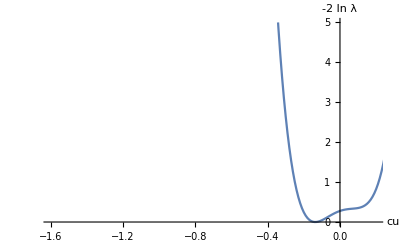

```mathematica
i=3;
Clear[a,b,c,d,e,x];
bfl={-0.5,0,-0.5,-0.3,0};
bfu={0.5,2.5,0.5,-0.05,0.35};
{a,b,c,d,e}=ReplacePart[bf,i->x];
PointList={};
For[x=bfl[[i]],x<=bfu[[i]],x=x+0.01,
mueft=muSM*ParaTable/.rule;
muvec=mueft-muhat;
expUncSym=Sqrt[Abs[expVGau+expVGauPrime*muvec]];
expCov=Table[expCorr[[j,k]]*expUncSym[[j]]*expUncSym[[k]],{j,1,11},{k,1,11}];
thUncSym=Sqrt[Abs[thVGau+thVGauPrime*muvec]];
thCov=Table[thCorr[[j,k]]*expUncSym[[j]]*expUncSym[[k]],{j,1,11},{k,1,11}];
cov=expCov+thCov;
invCov=LinearSolve[cov,IdentityMatrix[11]];
LogL=muvec.invCov.muvec;
AppendTo[PointList,{x,LogL}]
];
text={"cG×10^-3","cA×10^-3","cu","cHW","cWW-cB"};
scale={0.1,0.1,1,0.1,0.1};
xlist=Transpose[PointList][[1]];
Llist=Transpose[PointList][[2]];
minL=Min[Llist];
Llist2=Llist-minL;
PointList2=Transpose[{xlist*scale[[i]],Llist2}];
ListPlot[PointList2,Joined->True,AxesLabel->{text[[i]],"-2 ln λ"},PlotRange->{{-1.6,0.2},{0,5}}]
```